```mathematica
SetDirectory[NotebookDirectory[]];
```

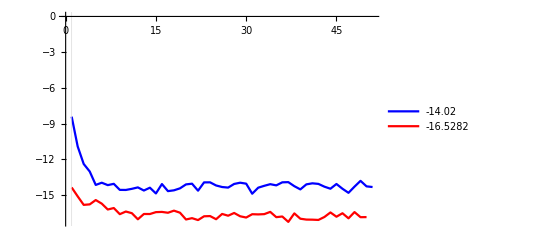

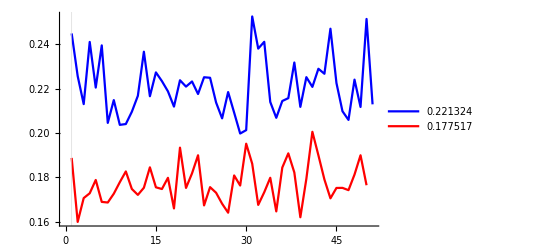

```mathematica
mmin=1;
corrdata=Import["nucmatip.dat"];
nocorrdata=Import["nucmatnoip.dat"];
corrE=Transpose[corrdata][[4]];
nocorrE=Transpose[nocorrdata][[4]];
corrσ=Transpose[corrdata][[6]];
nocorrσ=Transpose[nocorrdata][[6]];

corrl=Length[corrE];
nocorrl=Length[nocorrE];
ipmean=Mean[corrE[[mmin;;corrl]]];
nomean=Mean[nocorrE[[mmin;;nocorrl]]];
iperr=Sqrt[Total[corrσ[[mmin;;corrl]]^2]/Length[corrσ[[mmin;;corrl]]]];
noerr=Sqrt[Total[nocorrσ[[mmin;;nocorrl]]^2]/Length[nocorrσ[[mmin;;nocorrl]]]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
```

### Error Stuff

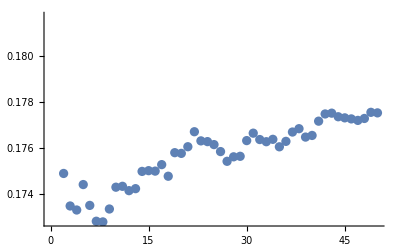

```mathematica
corrdata=Import["nucmatip.dat"];
nocorrdata=Import["nucmatnoip.dat"];
data=Import["nucmatip.dat"];
max=50;
error=Transpose[data][[6]][[1;;max]];

cumerr[indata_,n_]:=Module[{temp,aveerr},temp=indata[[1;;n]];
aveerr=Sqrt[Total[temp^2]/n];
aveerr]

plotdata=Range[1,max]*0;
For[i=1,i≤Length[error],i++,plotdata[[i]]={i,cumerr[error,i]};]

ListPlot[plotdata]
```